```mathematica
bases={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
roots=N[Sqrt[bases]]
```

{1.,1.41421,1.73205,2.,2.23607}

```mathematica
MetalN[n_]:=(n+Sqrt[n^2+4])/2
```

```mathematica
metals=N[MetalN[bases]]
```

{1.61803,2.41421,3.30278,4.23607,5.19258}

```mathematica
N[Sqrt[MetalN[Pi]+MetalN[Log2[Pi^E]]],50]
```

2.8521577095126531535727981912794589073178450824485

```mathematica
NumberForm[2.852157709512653,50]
```

2.852157709512653

```mathematica
N[28/11]
```

2.54545

```mathematica
Sqrt[MetalN[Pi]+MetalN[Log2[Pi^E]]]
```

√(1/2 (π+√(4+π^2))+1/2 ((ⅇ Log[π])/Log[2]+√(4+(ⅇ^2 Log[π]^2)/Log[2]^2)))

```mathematica
Simplify[Sqrt[MetalN[Pi]+MetalN[Log2[Pi^E]]]]
```

1/(√(Log[4]/(π Log[2]+√(4+π^2) Log[2]+ⅇ Log[π]+√(4 Log[2]^2+ⅇ^2 Log[π]^2))))

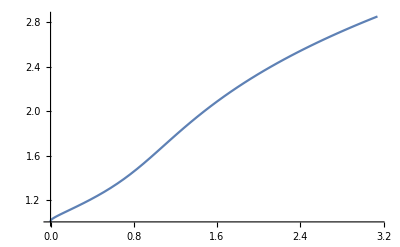

```mathematica
Plot[Sqrt[MetalN[x]+MetalN[Log2[x^E]]],{x,0,Pi}]
```

```mathematica
nffx=1
```

1

```mathematica
nffy=Sqrt[MetalN[Pi]+MetalN[Log2[Pi^E]]]
```

√(1/2 (π+√(4+π^2))+1/2 ((ⅇ Log[π])/Log[2]+√(4+(ⅇ^2 Log[π]^2)/Log[2]^2)))

```mathematica
sfux=37
```

37

```mathematica
sfuy=28
```

28

```mathematica
uatx=2
```

2

```mathematica
uaty=3
```

3

```mathematica
alcm=LCM[x[[1]],x[[2]],x[[3]]]
```

74

```mathematica
x={1,37,2}
```

{1,37,2}

```mathematica
y={Sqrt[MetalN[Pi]+MetalN[Log2[Pi^E]]],28,3}
```

{√(1/2 (π+√(4+π^2))+1/2 ((ⅇ Log[π])/Log[2]+√(4+(ⅇ^2 Log[π]^2)/Log[2]^2))),28,3}

```mathematica
tuub=(alcm/x)*y
```

{74 √(1/2 (π+√(4+π^2))+1/2 ((ⅇ Log[π])/Log[2]+√(4+(ⅇ^2 Log[π]^2)/Log[2]^2))),56,111}

```mathematica
alsm=Total[tuub]
```

167+74 √(1/2 (π+√(4+π^2))+1/2 ((ⅇ Log[π])/Log[2]+√(4+(ⅇ^2 Log[π]^2)/Log[2]^2)))

```mathematica
gdf={alcm/GCD[alcm,alsm],alsm/GCD[alcm,alsm]}
```

{74/GCD[74,167+74 √(1/2 (π+√(4+π^2))+1/2 ((ⅇ Log[π])/Log[2]+√(4+(ⅇ^2 Log[π]^2)/Log[2]^2)))],(167+74 √(1/2 (π+√(4+π^2))+1/2 ((ⅇ Log[π])/Log[2]+√(4+(ⅇ^2 Log[π]^2)/Log[2]^2))))/GCD[74,167+74 √(1/2 (π+√(4+π^2))+1/2 ((ⅇ Log[π])/Log[2]+√(4+(ⅇ^2 Log[π]^2)/Log[2]^2)))]}

```mathematica
N[gdf]
```

GCD::exact: GCD[74.,378.06]の引数74.は厳密数ではありません．

{74./GCD[74.,378.06],378.06/GCD[74.,378.06]}

```mathematica
N[alsm,50]
```

378.05967050393633336438706615467995914152053610119

```mathematica
temp={1,(N[Sqrt[MetalN[Pi]+MetalN[Log2[Pi^E]]],50])}
```

{1,2.8521577095126531535727981912794589073178450824485}

```mathematica
temp={1,(N[Sqrt[MetalN[E]+MetalN[Log2[E^E]]],50])}
```

{1,2.6848556445831874173040538790714282523812685614953}

```mathematica
temp*200
```

{200,570.43154190253063071455963825589178146356901648971}

```mathematica
{200,536.9711289166374834608107758142856504762537122990512815952664`50.}
```

{200,536.97112891663748346081077581428565047625371229905}

```mathematica
temp*70
```

{70,187.93989512082311921128377153499997766668879930467}

```mathematica
bs={11,28}
```

{11,28}

```mathematica
N[bs*(200/11)]
```

{200.,509.091}

```mathematica
const:=Sqrt[MetalN[E]+MetalN[Log2[E^E]]]
```

```mathematica
const
```

√(1/2 (ⅇ+√(4+ⅇ^2))+1/2 (√(4+ⅇ^2/Log[2]^2)+ⅇ/Log[2]))

```mathematica
N[const]
```

2.68486

```mathematica
c2=const*74-(56+111)
```

-167+74 √(1/2 (ⅇ+√(4+ⅇ^2))+1/2 (√(4+ⅇ^2/Log[2]^2)+ⅇ/Log[2]))

```mathematica
N[c2]
```

31.6793

```mathematica
px={74,N[c2]}*(200/74)
```

{200,85.6198}

```mathematica
px=N[(({74,(74*const-(56+111))*3}*(200/74))-({10,10}*2))*{1,1/5}-{0,4},50]
```

{180.,43.37186653917167926567565467776057947494141656862}

```mathematica
{74,95.03795309746760664149996115385707202864162065194692257075513395562448446946333`50.}*
```

```mathematica
56.859332/2
```

28.4297

```mathematica
256.859332-20
```

236.859

```mathematica
180/3
```

60